## Basic definitions

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"pauliStringsHandler.m"}]];

SetOptions[$FrontEndSession,"ExportTypesetOptions"->{"PageWidth"->500}]
SelectPositions=ResourceFunction["SelectPositions"];

simplifyIdentities=StringReplace["I"..->"I"];

groupByFirst[pauliStrings_List,n_Integer]:=GatherBy[pauliStrings,StringTake[#,n]&];

sortString[s_String]:=StringJoin@Sort@Characters@s;
sortPair[{a_List,b_List}]:=With[{ord=Ordering[a]},
{a[[ord]],b[[ord]]}
];
sortPair[{a_String,b_String}]:=StringJoin/@sortPair[{Characters@a,Characters@b}]
sortPairUnordered[{a_,b_}]:=First@Sort@{sortPair@{a,b},sortPair@{b,a}};

canonPair[{a_List,b_List}]:=First@Sort@{
Transpose@SortBy[Thread[{a,b}],{First,Last}],
Transpose@SortBy[Thread[{b,a}],{First,Last}]
};
canonPair[{a_String,b_String}]:=StringJoin/@canonPair[{Characters@a,Characters@b}];

ClearAll[noRepeatedIs];
noRepeatedIs[gens:{__String}]:=With[{numGens=Length@gens},
Not@MemberQ[Transpose[Characters/@gens],ConstantArray["I",numGens]]
];

findGensWithMostIs[gens:{__String}]:=MaximalBy[
Subsets[Rest@allStringsFromAbGenerators@gens,{Length@gens}],
(Count[MemberQ[#,"I"]&/@Transpose[Characters/@#],True]&)
][[1]];
supercanonPair[gens:{_String,_String}]:=ReplaceAll[
Transpose[Characters/@gens],
{
{"I","Y"}->{"I","X"},
{"Y","I"}->{"X","I"},
{"Y","Y"}->{"X","X"},
{"Y","Z"}->{"X","Z"},
{"Z","Y"}->{"Z","X"},
{"Y","X"}->{"X","Y"}
}
]//Transpose//Map@StringJoin;

zFreeCentralizerFromGenerators[h_String]:=With[{t=StringLength@h},
Plus[
3^t,
3^StringCount[h,"I"]*(-1)^StringCount[h,"Z"]
]/2
];

zFreeCentralizerFromGenerators[h1_String,h2_String]:=With[{t=StringLength@h1},Plus[
3^t,
3^StringCount[h1,"I"]*(-1)^StringCount[h1,"Z"],
3^StringCount[h2,"I"]*(-1)^StringCount[h2,"Z"],
Times[
3^Length@Cases[Equal@@@#&@Thread@{Characters[h1],Characters[h2]},True],
(-1)^Length@Select[Thread@{Characters@h1,Characters@h2},#=={"Z","I"}||#=={"I","Z"}||#=={"X","Y"}||#=={"Y","X"}&]
]
]/4];

zFreeCentralizerFromGenerators[strings_List]:=zFreeCentralizerFromGenerators@@strings;

randomStabiliserGroup[n_Integer]:=Module[{allstrings,group,randomIndex},
allstrings=Rest@allPauliStrings[n];
group={};
Do[
randomIndex=RandomInteger@{1,Length@allstrings};
AppendTo[group,allstrings[[randomIndex]]];
If[idx==n,Break[]];
allstrings=Drop[allstrings,{randomIndex}];
allstrings=Select[allstrings,paulisCommuteQ[#,group[[-1]]]&],
{idx,n}
];
group
];
```

```mathematica
countRowsWithZ[listOfCosets_List]:=Map[Length@*Select[StringContainsQ[#,"Z"]&],listOfCosets];
sortByZ[listOfCosets_List]:=Map[SortBy[StringContainsQ[#,"Z"]&],listOfCosets];
fullRankQ[listOfCosets_List]:=With[{m=Length@listOfCosets},
countNonZFullRows@listOfCosets==m
];

rowIsNotZFull[paulis_List]:=Or@@Table[Not@StringContainsQ[elem,"Z"],{elem,paulis}];
countNonZFullRows[listOfCosets_List]:=Length[Select[listOfCosets,rowIsNotZFull]];
povmRank[generators:{__String}]:=countNonZFullRows@stabiliserFromGenerators@generators;

haveAllIInSomeCol[listOfCosets_List]:=With[{chars=Characters/@listOfCosets},
Or@@Table[
AllTrue[col,#=="I"&],
{col,Transpose@chars}
]
];

(* these functions are used to take the generators of the coset and associated them suitably to the n qubit strings *)
attachPaulisToCosets[listOfPaulis_List,cosets_List]:=Transpose@{listOfPaulis,cosets}//Map[
Table[StringJoin[#[[1]],op],{op,#[[2]]}]&
];

associateCosetsToPaulis[cosets_List]:=With[{
t=StringLength@First@Flatten@cosets,
l=Log2[Length@First@cosets]
},
Module[{mat1,mat2,allPaulis,permutation},
allPaulis=allPauliStrings[t-l];
mat1=Boole@Outer[paulisCommuteQ,#,#]&@First@Transpose@cosets;
mat2=Boole@Outer[paulisCommuteQ,#,#]&@allPaulis;
permutation=Values@FindGraphIsomorphism[AdjacencyGraph@mat1,AdjacencyGraph@mat2][[1]];
attachPaulisToCosets[allPaulis[[permutation]],cosets]
]
];

associateCosetsToPaulis[cosets_List,n_Integer]:=With[{
t=StringLength@First@Flatten@cosets,
l=Log2[Length@First@cosets]
},
Module[{mat1,mat2,allPaulis,permutations},
allPaulis=allPauliStrings[t-l];
mat1=Boole@Outer[paulisCommuteQ,#,#]&@First@Transpose@cosets;
mat2=Boole@Outer[paulisCommuteQ,#,#]&@allPaulis;
permutations=Values/@FindGraphIsomorphism[AdjacencyGraph@mat1,AdjacencyGraph@mat2,n];
Table[
attachPaulisToCosets[allPaulis[[permutation]],cosets],
{permutation,permutations}
]
]
];

fullGeneratorsFromCosetsGenerators[cosetsGens_List]:=associateCosetsToPaulis[
stabiliserFromGenerators@cosetsGens
]//Flatten//independentGenerators;

fullGeneratorsFromCosetsGenerators[cosetsGens_List,n_Integer]:=Table[
fullCoset//Flatten//independentGenerators,
{fullCoset,associateCosetsToPaulis[stabiliserFromGenerators@cosetsGens,n]}
];

ClearAll[letterToPauli];
letterToPauli["I"]=IdentityMatrix[2];
letterToPauli["X"]=PauliMatrix[1];
letterToPauli["Y"]=PauliMatrix[2];
letterToPauli["Z"]=PauliMatrix[3];

ClearAll[pauliStringToMatrix];
pauliStringToMatrix[str_String?StringQ]/;StringMatchQ[str,RegularExpression["[IXYZ]+"]]:=KroneckerProduct@@(letterToPauli/@Characters[str]);

ClearAll[eigenSign];
eigenSign[U_,vec_,tol_:10^-10]:=With[{w=Chop[U.vec,tol]},
Which[
Chop[w-vec,tol]===ConstantArray[0,Length@w],1,
Chop[w+vec,tol]===ConstantArray[0,Length@w],-1,
True,0]
];

ClearAll[getPauliStrings,stabilizerCandidates,signatureMatrix,independentGenerators,ketToStabilizerGenerators];

getPauliStrings[n_Integer]:=DeleteCases[StringJoin@@#&/@Tuples[{"I","X","Y","Z"},n],StringRepeat["I",n]];

stabilizerCandidates[states_List]:=With[
{paulis=getPauliStrings@Log2@Length@First@states},
Select[paulis,
With[{U=pauliStringToMatrix@#},
AllTrue[states,eigenSign[U,#]=!=0&]
]&
]
];

binaryRank[M_List]:=If[M==={},0,With[{b=Mod[(1-M)/2,2]},Count[RowReduce[b,Modulus->2],_?(#=!=ConstantArray[0,Length@First[b]]&)]]];

ClearAll[signatureMatrix];
signatureMatrix[candidates_List,states_List]:=Table[eigenSign[pauliStringToMatrix[s],ψ],{s,candidates},{ψ,states}];


ClearAll[ketToStabilizerGenerators];
ketToStabilizerGenerators[states:{__List}]:=Module[{d=Length@First@states,n,gens,sig},
(*dimension check:all kets same length& dim=2^n*)
If[!SameQ@@(Length/@states),
Message[ketToStabilizerGenerators::dim,"non‑uniform lengths"];
Return[$Failed]
];
n=Log2[d];
If[!IntegerQ@n,
Message[ketToStabilizerGenerators::dim,"dimension not 2^n"];
Return[$Failed]
];
(*orthonormality check (numerical tolerance 10^-10)*)
If[Max[Abs[states.ConjugateTranspose[states]-IdentityMatrix[Length@states]]]>10^-10,
Message[ketToStabilizerGenerators::orth,"orthogonality check"];
Return[$Failed]
];
gens=stabilizerCandidates[states];
sig=signatureMatrix[gens,states];
independentGenerators[gens,sig]
];

randomLinearCombination[stuff_List]:=Total[
RandomReal[{0,1},Length@stuff]*stuff
];
statesFromAbelianGenerators[gens:{__String}]:=With[{
linearCombination=randomLinearCombination[pauliStringToMatrix/@gens]
},
Chop@Eigensystem[linearCombination][[2]]
];

(* —utility:translate a Pauli string to its 2 n‑bit binary vector—*)
pauliMap=<|"I"->{0,0},"X"->{1,0},"Y"->{1,1},"Z"->{0,1}|>;
pauliVec[str_String]:=Flatten[Characters[str]/. pauliMap];

ClearAll[independentGenerators]
independentGenerators::dim="All Pauli strings must have the same length.";
independentGenerators[strings_List]/;VectorQ[strings,StringQ]:=Module[{len,vecs,result},
len=DeleteDuplicates[StringLength/@strings];
If[len=!={len[[1]]},
Message[independentGenerators::dim];Return[$Failed]
];
(*2 ▸ binary vectors for each string*)
vecs=pauliVec/@strings;
(*3 ▸ stream through vecs,collect those that raise the rank over GF(2)*)
result=Fold[
Function[{state,pair},
Module[{basis=state[[1]],idxs=state[[2]],v=pair[[1]],i=pair[[2]]},
If[
MatrixRank[Append[basis,v],Modulus->2]>Length[basis],
{Append[basis,v],Append[idxs,i]},
state
]
]
],
{{},{}},
MapIndexed[{#1,#2[[1]]}&,vecs]
][[2]];
(*we only need kept indices*)
strings[[result]]
];


ClearAll[multiplyFromTo];
multiplyFromTo[paulis:{__String},startingPos_Integer,targetPoss_List]:=ReplacePart[
paulis,
Table[
targetPos->pauliProd[paulis[[startingPos]],paulis[[targetPos]]],
{targetPos,targetPoss}
]
];
multiplyFromTo[paulis:{__String},startingPos_Integer->targetPoss_List]:=multiplyFromTo[
paulis,startingPos,targetPoss
];
multiplyFromTo[paulis:{__String},startingPos_Integer,targetPos_Integer]:=multiplyFromTo[
paulis,startingPos,{targetPos}
];
multiplyFromTo[paulis:{__String},startingPos_Integer->targetPos_Integer]:=multiplyFromTo[
paulis,startingPos->{targetPos}
];
multiplyFromTo[chars:{{__String}..},args__]:=Characters/@multiplyFromTo[StringJoin/@chars,args];

multiplyFromTo[startingPos_->targetPoss_List][paulis_]:=multiplyFromTo[paulis,startingPos,targetPoss];

applyStoCol[characters_List]:=characters/.{"X"->"Y","Y"->"X"};
applyHtoCol[characters_List]:=characters/.{"X"->"Z","Z"->"X"};

ClearAll[localSgate];
localSgate[paulis:{__String},pos_Integer]:=With[{chars=Characters/@paulis},
StringJoin/@(Transpose@ReplacePart[Transpose@chars,
pos->applyStoCol@chars[[All,pos]]
])
];
localSgate[paulis:{__String},poss_List]:=With[{chars=Characters/@paulis},
StringJoin/@(Transpose@ReplacePart[Transpose@chars,
Table[pos->applyStoCol@chars[[All,pos]],{pos,poss}]
])
];
localSgate[chars:{{__String}..},pos_]:=Characters/@localSgate[StringJoin/@chars,pos];

localSgate[pos_Integer][paulis_]:=localSgate[paulis,pos];
localSgate[poss_List][paulis_]:=localSgate[paulis,poss];

ClearAll[localHgate];
localHgate[paulis:{__String},pos_Integer]:=With[{chars=Characters/@paulis},
StringJoin/@(Transpose@ReplacePart[Transpose@chars,
pos->applyHtoCol@chars[[All,pos]]
])
];
localHgate[paulis:{__String},poss_List]:=With[{chars=Characters/@paulis},
StringJoin/@(Transpose@ReplacePart[Transpose@chars,
Table[pos->applyHtoCol@chars[[All,pos]],{pos,poss}]
])
];
localHgate[chars:{{__String}..},pos_]:=Characters/@localHgate[StringJoin/@chars,pos];
localHgate[pos_Integer][paulis_]:=localHgate[paulis,pos];
localHgate[poss_List][paulis_]:=localHgate[paulis,poss];

echoPaulisCol[arg_]:=Echo[arg,"",prettifyPaulis@*Column];


ClearAll[findXYatCol,findYatCol,fixXYatCol];
findXYatCol[characters:{{__String}..},col_Integer]:=With[{colChars=characters[[All,col]]},
Flatten@SelectPositions[colChars,StringContainsQ[#,"X"|"Y"]&]
];
findYatCol[characters:{{__String}..},col_Integer]:=With[{colChars=characters[[All,col]]},
Flatten@SelectPositions[colChars,StringContainsQ[#,"Y"]&]
];

fixXYatCol[characters:{{__String}..},col_Integer,availableGens:{__Integer},appliedH_:False,bePedantic_:False]:=Module[
{xyposs=findXYatCol[characters,col],intersection,pivot},
intersection=Intersection[xyposs,availableGens];
If[bePedantic,
Echo[characters,"yo i'm here",Row@{prettifyPaulis@Column[StringJoin/@#],col,availableGens,appliedH}&]
];

If[intersection=={},
If[
appliedH==True,
Print["This shouldn't happen! There's no available gens to fix some X/Ys at col "<>ToString@col];
Print[prettifyPaulis@Column[StringJoin/@characters]];
Print["Available gens: "<>ToString@availableGens];
Abort[],
(* otherwise try to apply H as we haven't already done that *)
If[bePedantic,
Echo[col,"Applying H at col "<>ToString@col]
];
fixXYatCol[localHgate[characters,col],col,availableGens,True]
],
(* if we're here, there's a non empty intersection, so move along... *)
Which[
Length@xyposs>=2,
(* there's at least 2 generators with X/Y *)
pivot=intersection[[1]];
If[bePedantic,
Echo[pivot,"Using as pivot:"]
];
{
multiplyFromTo[characters,pivot->DeleteCases[xyposs,pivot]],
DeleteCases[availableGens,pivot],
appliedH
},
(* if there's 1 generator with X/Y, do nothing (return untouched characters), but still count the generator as "used" *)
Length@xyposs==1,
{characters,DeleteCases[availableGens,xyposs[[1]]],appliedH},
True,
(* if we're here, presumably some column contains NO X/Y; we can apply an H then to fix it *)
If[appliedH==True,
Print["This shouldn't happen: there seems to be 0 X/Ys (even after applying an H) at col "<>ToString@col];
Abort[],
(* otherwise apply H and move on *)
fixXYatCol[localHgate[characters,col],col,availableGens,True]
]
]
]
];

ClearAll[fixStrayYs];
fixStrayYs[characters:{{__String}..}]:=Module[
{rollingChars=characters,YsInCol,whereWeAppliedS={}},
Do[
YsInCol=Cases[rollingChars[[All,col]],"Y"];
Which[
(* if there's a single Y we fix it and remember where we applied the S *)
Length@YsInCol==1,
AppendTo[whereWeAppliedS,col];
rollingChars=localSgate[rollingChars,col],
(* check that there isn't more than 1 Y, which shouldn't happen *)
Length@YsInCol>1,
Print["This shouldn't happen; there should either 0 or 1 Y for each column (failed at col "<>ToString@col<>")"];
Return@$Failed
],
{col,Length@First@characters}
];
{rollingChars,whereWeAppliedS}
];

ClearAll[sortGeneratorsByXPosition];
sortGeneratorsByXPosition[generators:{__String}]:=generators//SortBy[StringContainsQ[#,"X"]&&StringPosition[#,"X"][[1]]&];

ClearAll[convertToGraphState];
Options[convertToGraphState]={"bePedantic"->False,"systemQubits"->None};
convertToGraphState[generators:{__String},OptionsPattern[]]:=With[{numQubits=StringLength@First@generators},
Module[{
rollingChars=Characters/@generators,
availableGens=Range@Length@generators,
whereWeAppliedH={},appliedH,whereWeAppliedS={}
},
Do[
{rollingChars,availableGens,appliedH}=fixXYatCol[rollingChars,col,availableGens,False,OptionValue@"bePedantic"];
If[appliedH==True,AppendTo[whereWeAppliedH,col]],
{col,Reverse@Range@Length@First@rollingChars}
];
{rollingChars,whereWeAppliedS}=fixStrayYs[rollingChars];
<|
"generators"->sortGeneratorsByXPosition[StringJoin/@rollingChars],
"H"->ReplacePart[ConstantArray[False,numQubits],Thread@Rule[whereWeAppliedH,True]],
"S"->ReplacePart[ConstantArray[False,numQubits],Thread@Rule[whereWeAppliedS,True]],
"labels"->Range@numQubits,
If[OptionValue@"systemQubits"=!=None,"systemQubits"->OptionValue@"systemQubits",{}]
|>
]
];


ClearAll[adjacencyGraphFromPaulis];
adjacencyGraphFromPaulis[graphState_Association]:=With[{
adjacencyMatrix=ReplaceAll[Characters/@sortGeneratorsByXPosition@graphState["generators"],{"I"->0,"X"->0,"Z"->1}],
labels=If[KeyExistsQ[graphState,"labels"],graphState@"labels",Range@StringLength@First@graphState["generators"]],
systemQubits=If[KeyExistsQ[graphState,"systemQubits"],graphState["systemQubits"],Print["Warning: you didn't specify the system qubits! Used {1} as default"];{1}]
},
AdjacencyGraph[adjacencyMatrix,
VertexLabels->Table[
idx->Row@{
labels[[idx]],
Sequence@@If[graphState["S"][[idx]],
{Style["(S)",Bold,Red]},
{}
],
Sequence@@If[graphState["H"][[idx]],
{Style["(H)",Bold,Blue]},
{}
]
},
{idx,Range@Length@labels}
],
GraphLayout->"CircularEmbedding",
VertexStyle->Table[qubit->Red,{qubit,systemQubits}],
VertexSize->Table[qubit->0.1,{qubit,systemQubits}]
]
];
```

## Generators for centralizers used to characterize the reachability conditions

## n=1, t=2

```mathematica
stabiliserFromGenerators@{"ZX"}//prettifyPaulis//Grid
```

II | ZX
IX | ZI
YY | XZ
XY | YZ

```mathematica
stabiliserFromGenerators@{"XZ"}//prettifyPaulis//Grid
```

II | XZ
XI | IZ
YY | ZX
YX | ZY

```mathematica
stabiliserFromGenerators@{"YZ"}//prettifyPaulis//Grid
```

II | YZ
XX | ZY
YI | IZ
XY | ZX

```mathematica
stabiliserFromGenerators@{"YY"}//prettifyPaulis//Grid
```

II | YY
XX | ZZ
IY | YI
XZ | ZX

## n=2, t=3

```mathematica
stabiliserFromGenerators@{"ZZ"}//fullRankQ
stabiliserFromGenerators@{"ZX"}//fullRankQ
```

False

True

How many inequivalent nontrivial generators are there?

```mathematica
inequivalentGenerators3q=DeleteDuplicates[sortString/@Rest@allPauliStrings@3]
inequivalentGenerators3q//Length
```

{IIX,IIY,IIZ,IXX,IXY,IXZ,IYY,IYZ,IZZ,XXX,XXY,XXZ,XYY,XYZ,XZZ,YYY,YYZ,YZZ,ZZZ}

19

```mathematica
inequivalentGenerators3q=Select[DeleteDuplicates[sortString/@Rest@allPauliStrings@3],Not@StringContainsQ[#,"Y"]&];
Rule[#,GatherBy[#,Sort@*Characters]&@Flatten@stabiliserFromGenerators@{#}]&/@inequivalentGenerators3q//prettifyPaulis//Map[#[[1]]->Column@#[[2]]&]
```

{IIX→{III}
{IIX,XII,IXI}
{XIX,IXX,XXI}
{XXX}
{ZII,IZI}
{ZIX,ZXI,IZX,XZI}
{YII,IYI}
{YIX,YXI,IYX,XYI}
{ZXX,XZX}
{YXX,XYX}
{ZZI}
{ZZX}
{YZI,ZYI}
{YZX,ZYX}
{YYI}
{YYX},IIZ→{III}
{IIZ,ZII,IZI}
{XII,IXI}
{XIZ,IXZ,ZXI,XZI}
{XXI}
{XXZ}
{ZIZ,IZZ,ZZI}
{YII,IYI}
{YIZ,IYZ,YZI,ZYI}
{ZXZ,XZZ}
{YXI,XYI}
{YXZ,XYZ}
{ZZZ}
{YZZ,ZYZ}
{YYI}
{YYZ},IXX→{III}
{IXX,XIX,XXI}
{XII,IIX,IXI}
{XXX}
{ZII}
{ZXX}
{YII}
{YXX}
{ZIX,ZXI}
{YIX,YXI}
{IYY}
{IZZ}
{XYY}
{XZZ}
{IYZ,IZY}
{XYZ,XZY}
{ZYY,YYZ,YZY}
{ZZZ}
{YYY}
{YZZ,ZYZ,ZZY},IXZ→{III}
{IXZ,XIZ,ZXI,IZX}
{XII,IXI}
{XXZ,XZX}
{IIZ,ZII}
{XXI}
{ZXZ,ZZX}
{YII}
{YXZ,XZY,YZX,ZYX}
{ZIZ}
{YXI,IYX}
{YIZ,IZY}
{IYY}
{XYY,YYX}
{XYX}
{ZYY,YZY}
{YYY}
{ZZY},IZZ→{III}
{IZZ,ZIZ,ZZI}
{XII}
{XZZ}
{IXX}
{IYY}
{XXX}
{XYY,YXY,YYX}
{ZII,IIZ,IZI}
{ZZZ}
{YII}
{YZZ}
{ZXX}
{ZYY}
{YXX,XXY,XYX}
{YYY}
{XIZ,XZI}
{IXY,IYX}
{YIZ,YZI}
{ZXY,ZYX},XXX→{III}
{XXX}
{IXX,XIX,XXI}
{XII,IXI,IIX}
{YYX,YXY,XYY}
{ZZI,ZIZ,IZZ}
{YZI,ZYI,YIZ,ZIY,IYZ,IZY}
{ZYX,YZX,ZXY,YXZ,XZY,XYZ}
{YYI,YIY,IYY}
{ZZX,ZXZ,XZZ},XXZ→{III}
{XXZ,ZXX,XZX}
{XII,IXI}
{IXZ,XIZ,ZIX,IZX}
{XXI}
{IIZ}
{YXY,XYY}
{YIX,IYX}
{ZXY,XZY}
{YIY,IYY,YYI}
{YXX,XYX}
{ZIY,IZY,YZI,ZYI}
{YYZ}
{ZZI}
{ZYZ,YZZ}
{ZZZ},XZZ→{III}
{XZZ,ZXZ,ZZX}
{XII}
{IZZ}
{IXX}
{XYY}
{IYY,YYI,YIY}
{XXX}
{YYZ,YZY}
{ZXI,ZIX,XIZ,XZI}
{YXI,YIX,IYX,IXY}
{ZYZ,ZZY}
{IZI,IIZ}
{XXY,XYX}
{YXZ,YZX}
{ZYI,ZIY},ZZZ→{III}
{ZZZ}
{XXI,XIX,IXX}
{YYZ,YZY,ZYY}
{IZZ,ZIZ,ZZI}
{ZII,IZI,IIZ}
{YXI,YIX,XYI,IYX,XIY,IXY}
{XYZ,XZY,YXZ,ZXY,YZX,ZYX}
{IYY,YIY,YYI}
{ZXX,XZX,XXZ}}

```mathematica
With[{inequivalentGenerators3qNoY=Select[DeleteDuplicates[sortString/@allPauliStrings@3],True(*Not@StringContainsQ[#,"Y"]*)&]},
Table[
Rule[s,
Row@{zFreeCentralizerFromGenerators@s,", rank=",countNonZFullRows@stabiliserFromGenerators@{s}}
],
{s,inequivalentGenerators3qNoY}
]//SortBy@Last//SplitBy[#,Last]&//Map[Rule[First/@#,Framed@#[[1,2]]]&]//Column//prettifyPaulis
]
```

{IIZ}→9, rank=9
{IXZ,IYZ}→12, rank=12
{XXZ,XYZ,YYZ,ZZZ}→13, rank=13
{XXX,XXY,XYY,XZZ,YYY,YZZ}→14, rank=10
{IXX,IXY,IYY,IZZ}→15, rank=9
{IIX,IIY}→18, rank=9
{III}→27, rank=27

```mathematica
stabiliserFromGenerators@{"XZZ"}//Column//prettifyPaulis
```

{III,XZZ}
{XII,IZZ}
{IXX,XYY}
{IYY,XXX}
{YYZ,ZXI}
{YXI,ZYZ}
{YZY,ZIX}
{YIX,ZZY}
{IZI,XIZ}
{IIZ,XZI}
{IYX,XXY}
{IXY,XYX}
{YXZ,ZYI}
{YYI,ZXZ}
{YIY,ZZX}
{YZX,ZIY}

## n=3, t=4

```mathematica
With[{
sortedStringsNoY=Select[DeleteDuplicatesBy[sortString]@Rest@allPauliStrings[4],Not@StringContainsQ[#,"Y"]&]
},
Table[
countNonZFullRows@stabiliserFromGenerators@{s},
{s,sortedStringsNoY}
]//DeleteDuplicates//Sort
]
```

{27,30,33,36,39,40}

```mathematica
bestGeneratorst4=With[{
sortedStringsNoY=Select[DeleteDuplicatesBy[sortString]@Rest@allPauliStrings[4],Not@StringContainsQ[#,"Y"]&]
},
Select[sortedStringsNoY,
zFreeCentralizerFromGenerators@#==40&
]
]
```

{XXXZ,XZZZ}

```mathematica
Table[
Rule[s,
stabiliserFromGenerators@{s}//Flatten//Select[Not@StringContainsQ[#,"Z"]&]//Length
],
{s,allPauliStrings[4]}
]//SortBy@Last//SplitBy[#,Last]&//Map[Rule[First/@#,Framed@#[[1,2]]]&]//Column//prettifyPaulis
```

{IIIZ,IIZI,IZII,ZIII}→27
{IIXZ,IIYZ,IIZX,IIZY,IXIZ,IXZI,IYIZ,IYZI,IZIX,IZIY,IZXI,IZYI,XIIZ,XIZI,XZII,YIIZ,YIZI,YZII,ZIIX,ZIIY,ZIXI,ZIYI,ZXII,ZYII}→36
{IXXZ,IXYZ,IXZX,IXZY,IYXZ,IYYZ,IYZX,IYZY,IZXX,IZXY,IZYX,IZYY,IZZZ,XIXZ,XIYZ,XIZX,XIZY,XXIZ,XXZI,XYIZ,XYZI,XZIX,XZIY,XZXI,XZYI,YIXZ,YIYZ,YIZX,YIZY,YXIZ,YXZI,YYIZ,YYZI,YZIX,YZIY,YZXI,YZYI,ZIXX,ZIXY,ZIYX,ZIYY,ZIZZ,ZXIX,ZXIY,ZXXI,ZXYI,ZYIX,ZYIY,ZYXI,ZYYI,ZZIZ,ZZZI}→39
{XXXZ,XXYZ,XXZX,XXZY,XYXZ,XYYZ,XYZX,XYZY,XZXX,XZXY,XZYX,XZYY,XZZZ,YXXZ,YXYZ,YXZX,YXZY,YYXZ,YYYZ,YYZX,YYZY,YZXX,YZXY,YZYX,YZYY,YZZZ,ZXXX,ZXXY,ZXYX,ZXYY,ZXZZ,ZYXX,ZYXY,ZYYX,ZYYY,ZYZZ,ZZXZ,ZZYZ,ZZZX,ZZZY}→40
{XXXX,XXXY,XXYX,XXYY,XXZZ,XYXX,XYXY,XYYX,XYYY,XYZZ,XZXZ,XZYZ,XZZX,XZZY,YXXX,YXXY,YXYX,YXYY,YXZZ,YYXX,YYXY,YYYX,YYYY,YYZZ,YZXZ,YZYZ,YZZX,YZZY,ZXXZ,ZXYZ,ZXZX,ZXZY,ZYXZ,ZYYZ,ZYZX,ZYZY,ZZXX,ZZXY,ZZYX,ZZYY,ZZZZ}→41
{IXXX,IXXY,IXYX,IXYY,IXZZ,IYXX,IYXY,IYYX,IYYY,IYZZ,IZXZ,IZYZ,IZZX,IZZY,XIXX,XIXY,XIYX,XIYY,XIZZ,XXIX,XXIY,XXXI,XXYI,XYIX,XYIY,XYXI,XYYI,XZIZ,XZZI,YIXX,YIXY,YIYX,YIYY,YIZZ,YXIX,YXIY,YXXI,YXYI,YYIX,YYIY,YYXI,YYYI,YZIZ,YZZI,ZIXZ,ZIYZ,ZIZX,ZIZY,ZXIZ,ZXZI,ZYIZ,ZYZI,ZZIX,ZZIY,ZZXI,ZZYI}→42
{IIXX,IIXY,IIYX,IIYY,IIZZ,IXIX,IXIY,IXXI,IXYI,IYIX,IYIY,IYXI,IYYI,IZIZ,IZZI,XIIX,XIIY,XIXI,XIYI,XXII,XYII,YIIX,YIIY,YIXI,YIYI,YXII,YYII,ZIIZ,ZIZI,ZZII}→45
{IIIX,IIIY,IIXI,IIYI,IXII,IYII,XIII,YIII}→54
{IIII}→81

```mathematica
With[{t=4,n=3},{(3^t-1)/2,(3^t+1)/2,4^n}]
```

{40,41,64}

## n=4, t=5

```mathematica
Table[
Rule[s,
stabiliserFromGenerators@{s}//Flatten//Select[Not@StringContainsQ[#,"Z"]&]//Length
],
{s,Select[allPauliStrings[5],Not@StringContainsQ[#,"I"]&]}
]//SortBy@Last//SplitBy[#,Last]&//Map[Rule[First/@#,Framed@#[[1,2]]]&]//Column//prettifyPaulis
```

{XXXXZ,XXXYZ,XXXZX,XXXZY,XXYXZ,XXYYZ,XXYZX,XXYZY,XXZXX,XXZXY,XXZYX,XXZYY,XXZZZ,XYXXZ,XYXYZ,XYXZX,XYXZY,XYYXZ,XYYYZ,XYYZX,XYYZY,XYZXX,XYZXY,XYZYX,XYZYY,XYZZZ,XZXXX,XZXXY,XZXYX,XZXYY,XZXZZ,XZYXX,XZYXY,XZYYX,XZYYY,XZYZZ,XZZXZ,XZZYZ,XZZZX,XZZZY,YXXXZ,YXXYZ,YXXZX,YXXZY,YXYXZ,YXYYZ,YXYZX,YXYZY,YXZXX,YXZXY,YXZYX,YXZYY,YXZZZ,YYXXZ,YYXYZ,YYXZX,YYXZY,YYYXZ,YYYYZ,YYYZX,YYYZY,YYZXX,YYZXY,YYZYX,YYZYY,YYZZZ,YZXXX,YZXXY,YZXYX,YZXYY,YZXZZ,YZYXX,YZYXY,YZYYX,YZYYY,YZYZZ,YZZXZ,YZZYZ,YZZZX,YZZZY,ZXXXX,ZXXXY,ZXXYX,ZXXYY,ZXXZZ,ZXYXX,ZXYXY,ZXYYX,ZXYYY,ZXYZZ,ZXZXZ,ZXZYZ,ZXZZX,ZXZZY,ZYXXX,ZYXXY,ZYXYX,ZYXYY,ZYXZZ,ZYYXX,ZYYXY,ZYYYX,ZYYYY,ZYYZZ,ZYZXZ,ZYZYZ,ZYZZX,ZYZZY,ZZXXZ,ZZXYZ,ZZXZX,ZZXZY,ZZYXZ,ZZYYZ,ZZYZX,ZZYZY,ZZZXX,ZZZXY,ZZZYX,ZZZYY,ZZZZZ}→121
{XXXXX,XXXXY,XXXYX,XXXYY,XXXZZ,XXYXX,XXYXY,XXYYX,XXYYY,XXYZZ,XXZXZ,XXZYZ,XXZZX,XXZZY,XYXXX,XYXXY,XYXYX,XYXYY,XYXZZ,XYYXX,XYYXY,XYYYX,XYYYY,XYYZZ,XYZXZ,XYZYZ,XYZZX,XYZZY,XZXXZ,XZXYZ,XZXZX,XZXZY,XZYXZ,XZYYZ,XZYZX,XZYZY,XZZXX,XZZXY,XZZYX,XZZYY,XZZZZ,YXXXX,YXXXY,YXXYX,YXXYY,YXXZZ,YXYXX,YXYXY,YXYYX,YXYYY,YXYZZ,YXZXZ,YXZYZ,YXZZX,YXZZY,YYXXX,YYXXY,YYXYX,YYXYY,YYXZZ,YYYXX,YYYXY,YYYYX,YYYYY,YYYZZ,YYZXZ,YYZYZ,YYZZX,YYZZY,YZXXZ,YZXYZ,YZXZX,YZXZY,YZYXZ,YZYYZ,YZYZX,YZYZY,YZZXX,YZZXY,YZZYX,YZZYY,YZZZZ,ZXXXZ,ZXXYZ,ZXXZX,ZXXZY,ZXYXZ,ZXYYZ,ZXYZX,ZXYZY,ZXZXX,ZXZXY,ZXZYX,ZXZYY,ZXZZZ,ZYXXZ,ZYXYZ,ZYXZX,ZYXZY,ZYYXZ,ZYYYZ,ZYYZX,ZYYZY,ZYZXX,ZYZXY,ZYZYX,ZYZYY,ZYZZZ,ZZXXX,ZZXXY,ZZXYX,ZZXYY,ZZXZZ,ZZYXX,ZZYXY,ZZYYX,ZZYYY,ZZYZZ,ZZZXZ,ZZZYZ,ZZZZX,ZZZZY}→122

```mathematica
{(3^5-1)/2,(3^5+1)/2,4^4}
```

{121,122,256}

```mathematica
stabiliserFromGenerators@{"XXZ"}//Thread[{"II","XI","IX","XX","ZI","YI","ZX","YX","IZ","XZ","IY","XY","ZZ","YZ","ZY","YY"}->#]&//SortBy@First//prettifyPaulis//Column
```

II→{III,XXZ}
IX→{IXI,XIZ}
IY→{IYX,XZY}
IZ→{XYY,IZX}
XI→{XII,IXZ}
XX→{XXI,IIZ}
XY→{XYX,IZY}
XZ→{IYY,XZX}
YI→{YIX,ZXY}
YX→{YXX,ZIY}
YY→{YYI,ZZZ}
YZ→{YZI,ZYZ}
ZI→{YXY,ZIX}
ZX→{YIY,ZXX}
ZY→{YZZ,ZYI}
ZZ→{YYZ,ZZI}

```mathematica
anticommutingSet[list_List]:=Subsets[list,{2}]//Map[Not@paulisCommuteQ@#&]//Apply@And
```

```mathematica
anticommutingSet/@Subsets[Flatten[stabiliserFromGenerators@{"ZZZ"}],{5}]
```

```mathematica
results=Subsets[Flatten[stabiliserFromGenerators@{"ZZZ"}],{5}]//Select@anticommutingSet;
```

```mathematica
results//Map[SortBy[StringContainsQ[#,"Z"]&]]//Map@Last//Select[Not@StringContainsQ[#,"Z"]&]
```

{}

## t=n+2

## n=2, t=4

```mathematica
pairsOfAbelian4qubitGenerators=Subsets[Rest@allPauliStrings[4],{2}]//Select[paulisCommuteQ]//DeleteDuplicatesBy@canonPair;
pairsOfAbelian4qubitGenerators//{Length@#,prettifyPaulis@#}&;

goodStabilisersGenst4=pairsOfAbelian4qubitGenerators//Select[fullRankQ@*stabiliserFromGenerators]//DeleteDuplicatesBy[Sort@*allStringsFromAbGenerators];
goodStabilisersGensNoYt4=Select[goodStabilisersGenst4,And@@(Not@StringContainsQ[#,"Y"]&/@Flatten@#)&];
```

```mathematica
stabiliserFromGenerators@{"XZII","IIXZ"}//prettifyPaulis//Grid
```

IIII | IIXZ | XZII | XZXZ
XIII | IZII | IZXZ | XIXZ
IIXI | IIIZ | XZIZ | XZXI
XIXI | IZIZ | IZXI | XIIZ
YYII | YYXZ | ZXII | ZXXZ
YXII | YXXZ | ZYII | ZYXZ
YYXI | YYIZ | ZXIZ | ZXXI
YXXI | YXIZ | ZYIZ | ZYXI
IIYY | IIZX | XZYY | XZZX
XIYY | IZYY | IZZX | XIZX
IIYX | IIZY | XZYX | XZZY
XIYX | IZYX | IZZY | XIZY
YYYY | YYZX | ZXYY | ZXZX
YXYY | YXZX | ZYYY | ZYZX
YYYX | YYZY | ZXYX | ZXZY
YXYX | YXZY | ZYYX | ZYZY

```mathematica
Table[
Rule[s,povmRank@s],
{s,pairsOfAbelian4qubitGenerators}
]//SortBy@Last//SplitBy[#,Last]&//Map[Rule[First[First/@#],Framed[Row@{#[[1,2]]," (",Length@#,")"}]]&]//Column//prettifyPaulis
```

{IIIX,IIXI}→9 (131)
{IIIX,XXXI}→10 (265)
{IIIX,IXZI}→12 (117)
{IIIX,XXZI}→13 (114)
{IIXZ,XXIZ}→14 (246)
{IXXZ,XIZX}→15 (64)
{IIXZ,XZII}→16 (50)

```mathematica
Table[
Rule[s,zFreeCentralizerFromGenerators@s],
{s,pairsOfAbelian4qubitGenerators}
]//SortBy@Last//SplitBy[#,Last]&//Map[Rule[First[First/@#],Framed[Row@{#[[1,2]]," (",Length@#,")"}]]&]//Column//prettifyPaulis
```

{IIIZ,IIZI}→9 (2)
{IIIZ,IXZI}→12 (6)
{IIIZ,XXZI}→13 (12)
{IIIZ,XXXI}→14 (18)
{IIIZ,IXXI}→15 (12)
{IIXZ,XZII}→16 (7)
{IIIX,IIZI}→18 (168)
{IXXZ,XIZX}→19 (64)
{IIXX,XZII}→20 (205)
{IIXX,IXYZ}→21 (73)
{IIXX,XXYZ}→22 (142)
{IIXX,XXYY}→23 (70)
{IIIX,IXZI}→24 (79)
{IIXX,XXII}→25 (26)
{IIIX,XXZI}→26 (24)
{IIXX,IIYY}→27 (12)
{IIIX,XXXI}→28 (36)
{IIIX,IXXI}→30 (24)
{IIIX,IIXI}→36 (7)

```mathematica
Select[pairsOfAbelian4qubitGenerators,noRepeatedIs]//Map[supercanonPair@*canonPair@*findGensWithMostIs]//DeleteDuplicates//Length
```

120

```mathematica
Select[pairsOfAbelian4qubitGenerators,noRepeatedIs]//Map[supercanonPair@*canonPair@*findGensWithMostIs]//Map@Column//prettifyPaulis
```

### List all good cases for 2+4

```mathematica
goodStabilisersGenst4
```

{{IIXZ,XZII},{IIXZ,YZII},{IIYZ,XZYZ},{IIYZ,YZII},{XXXX,YYYZ},{XXXX,YZZZ},{XXXY,YYYZ},{XXXY,YYZX},{XXXY,YZZZ},{XXXZ,YYYX},{XXXZ,YYYY},{XXXZ,YYZX},{XXXZ,YYZY},{XXXZ,YZZX},{XXXZ,YZZY},{XXYY,YYXZ},{XXYY,YZXX},{XXYY,YZZZ},{XXYY,ZZXZ},{XXYZ,YYXY},{XXYZ,YYZX},{XXYZ,YYZY},{XXYZ,YZXX},{XXYZ,YZXY},{XXYZ,YZZX},{XXYZ,YZZY},{XXYZ,ZZZY},{XXZZ,YZXY},{XXZZ,YZYY},{XYYY,YZZZ},{XYYY,ZXZZ},{XYYZ,YXZY},{XYYZ,YZZX},{XYYZ,YZZY},{XYYZ,ZXZY},{XYYZ,ZZZX},{XYYZ,ZZZY},{XYZZ,YZYY},{XZZZ,YYYY},{XZZZ,ZYYY}}

```mathematica
zFreeCentralizerFromGenerators/@Select[pairsOfAbelian4qubitGenerators,noRepeatedIs]//Sort
```

{13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,16,16,16,16,16,16,16,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,22,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,23,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,24,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,25,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,26,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28,28}

```mathematica
Select[pairsOfAbelian4qubitGenerators,noRepeatedIs]//GroupBy[zFreeCentralizerFromGenerators]//KeySort//Last
```

{{IIIX,XXXI},{IIIX,XXXX},{IIIX,XXYI},{IIIX,XXYX},{IIIX,XYYI},{IIIX,XYYX},{IIIX,XZZI},{IIIX,XZZX},{IIIX,YYYI},{IIIX,YYYX},{IIIX,YZZI},{IIIX,YZZX},{IIIY,XXXI},{IIIY,XXXY},{IIIY,XXYI},{IIIY,XXYY},{IIIY,XYYI},{IIIY,XYYY},{IIIY,XZZI},{IIIY,XZZY},{IIIY,YYYI},{IIIY,YYYY},{IIIY,YZZI},{IIIY,YZZY},{IXXX,XXXX},{IXXX,YXXX},{IXXY,XXXY},{IXXY,YXXY},{IXYY,XXYY},{IXYY,YXYY},{IXZZ,XXZZ},{IXZZ,YXZZ},{IYYY,XYYY},{IYYY,YYYY},{IYZZ,XYZZ},{IYZZ,YYZZ}}

```mathematica
goodStabilisersGenst4=pairsOfAbelian4qubitGenerators//Select[fullRankQ@*stabiliserFromGenerators]//DeleteDuplicatesBy[Sort@*allStringsFromAbGenerators];
goodStabilisersGensNoYt4=Select[goodStabilisersGenst4,And@@(Not@StringContainsQ[#,"Y"]&/@Flatten@#)&];
{goodStabilisersGenst4,goodStabilisersGensNoYt4}//Map@Length
```

{40,1}

```mathematica
goodStabilisersGenst4//Map[Rest@*allStringsFromAbGenerators]//Map[SortBy[StringCount[#,"Z"]&]]//Map[sortByZInCols]//SortBy[Map[StringCount[#,"Z"]&]]//GroupBy[Map[StringCount[#,"Z"]&]]//Map[prettifyPaulis@*Column,#,{2}]&
```

<|{0,1,3}→{XXXX
ZYYY
YZZZ,XXXX
ZYYY
YZZZ,XXXY
ZYYX
YZZZ,XXXY
ZYYX
YZZZ,XXXY
ZYYX
YZZZ,XXYY
ZYXX
YZZZ,XXYY
ZYXX
YZZZ,XXYY
ZYXX
YZZZ,XYYY
ZXXX
YZZZ,XYYY
ZXXX
YZZZ,YXXX
ZYYY
XZZZ,YXXX
ZYYY
XZZZ,YXXY
ZYYX
XZZZ,YXXY
ZYYX
XZZZ,YXXY
ZYYX
XZZZ,YXYY
ZYXX
XZZZ,YXYY
ZYXX
XZZZ,YYYY
ZXXX
XZZZ,YYYY
ZXXX
XZZZ},{1,1,2}→{IXZI
XIIZ
XXZZ,IXZI
YIIZ
YXZZ,IYZI
XIIZ
XYZZ,IYZI
YIIZ
YYZZ,ZXXX
XZYY
YYZZ,ZXXX
XZYY
YYZZ,ZXXX
YZYY
XYZZ,ZXXX
YZYY
XYZZ,ZXXY
XZYX
YYZZ,ZXXY
XZYX
YYZZ,ZXXY
YZYX
XYZZ,ZXXY
YZYX
XYZZ,ZXYY
XZXX
YYZZ,ZXYY
YZXX
XYZZ,ZYXX
XZYY
YXZZ,ZYXX
YZYY
XXZZ,ZYXY
XZYX
YXZZ,ZYXY
YZYX
XXZZ,ZYXY
YZYX
XXZZ,ZYYY
XZXX
YXZZ,ZYYY
YZXX
XXZZ}|>

```mathematica
goodStabilisersGenst4//Map[Rest@*allStringsFromAbGenerators]//Map[SortBy[StringCount[#,"Z"]&]]//Map[sortByZInCols]//SortBy[Map[StringCount[#,"Z"]&]]//Map@Column//prettifyPaulis
```

{XXXX
ZYYY
YZZZ,XXXX
ZYYY
YZZZ,XXXY
ZYYX
YZZZ,XXXY
ZYYX
YZZZ,XXXY
ZYYX
YZZZ,XXYY
ZYXX
YZZZ,XXYY
ZYXX
YZZZ,XXYY
ZYXX
YZZZ,XYYY
ZXXX
YZZZ,XYYY
ZXXX
YZZZ,YXXX
ZYYY
XZZZ,YXXX
ZYYY
XZZZ,YXXY
ZYYX
XZZZ,YXXY
ZYYX
XZZZ,YXXY
ZYYX
XZZZ,YXYY
ZYXX
XZZZ,YXYY
ZYXX
XZZZ,YYYY
ZXXX
XZZZ,YYYY
ZXXX
XZZZ,IXZI
XIIZ
XXZZ,IXZI
YIIZ
YXZZ,IYZI
XIIZ
XYZZ,IYZI
YIIZ
YYZZ,ZXXX
XZYY
YYZZ,ZXXX
XZYY
YYZZ,ZXXX
YZYY
XYZZ,ZXXX
YZYY
XYZZ,ZXXY
XZYX
YYZZ,ZXXY
XZYX
YYZZ,ZXXY
YZYX
XYZZ,ZXXY
YZYX
XYZZ,ZXYY
XZXX
YYZZ,ZXYY
YZXX
XYZZ,ZYXX
XZYY
YXZZ,ZYXX
YZYY
XXZZ,ZYXY
XZYX
YXZZ,ZYXY
YZYX
XXZZ,ZYXY
YZYX
XXZZ,ZYYY
XZXX
YXZZ,ZYYY
YZXX
XXZZ}

```mathematica
goodStabilisersGenst4//Map[canonPair@*supercanonPair@*canonPair@*supercanonPair@*canonPair@*findGensWithMostIs]//DeleteDuplicates//Sort//Echo//Map@Column//prettifyPaulis
```

{{IIXZ,XZII},{XXXX,YYYZ},{XXXX,YZZZ},{XXXZ,YYYX},{XXXZ,YYZX},{XXXZ,YZZX},{XXXZ,ZZZX}}

{IIXZ
XZII,XXXX
YYYZ,XXXX
YZZZ,XXXZ
YYYX,XXXZ
YYZX,XXXZ
YZZX,XXXZ
ZZZX}

```mathematica
Select[pairsOfAbelian4qubitGenerators,zFreeCentralizerFromGenerators@#==21&]//Map[Rest@*allStringsFromAbGenerators]//Map[SortBy[StringCount[#,"Z"]&]]//Map[sortByZInCols]//SortBy[Map[StringCount[#,"Z"]&]]//DeleteDuplicates//Map@Column//prettifyPaulis
```

{XXXX
YYYY
ZZZZ,XXXY
YYYX
ZZZZ,XXYY
YYXX
ZZZZ,XYYY
YXXX
ZZZZ,IIXX
IXZY
IXYZ,IIXX
IYZY
IYYZ,IIXY
IXZX
IXYZ,IIXY
IYZX
IYYZ,IIYX
IXZY
IXXZ,IIYX
IYZY
IYXZ,IIYY
IXZX
IXXZ,IIYY
IYZX
IYXZ,IXXI
XIXZ
XXIZ,IXXI
YIXZ
YXIZ,IXYI
XIYZ
XXIZ,IXYI
XXIZ
XIYZ,IXYI
YIYZ
YXIZ,IXYI
YXIZ
YIYZ,IYYI
XIYZ
XYIZ,IYYI
YIYZ
YYIZ,IXXI
IYYZ
IZZZ,IXYI
IYXZ
IZZZ,IYYI
IXXZ
IZZZ,XXXX
ZZYY
YYZZ,XXXY
ZZYX
YYZZ,XXYY
ZZXX
YYZZ,XYXX
ZZYY
YXZZ,XYXY
ZZYX
YXZZ,XYYY
ZZXX
YXZZ,YYXX
ZZYY
XXZZ,YYXY
ZZYX
XXZZ,YYYY
ZZXX
XXZZ,IXXZ
IYYZ
IZZI,IXYZ
IYXZ
IZZI,XXZI
XXIZ
IIZZ,XYZI
XYIZ
IIZZ,YYZI
YYIZ
IIZZ,ZZII
ZIZZ
IZZZ}

```mathematica
goodStabilisersGenst4//Map[Rest@*allStringsFromAbGenerators]//Map[SortBy[StringCount[#,"Z"]&]]//Map[sortByZInCols]//SortBy[Map[StringCount[#,"Z"]&]]//Map@Column//prettifyPaulis
```

```mathematica
goodStabilisersGenst4//Map@zFreeCentralizerFromGenerators
```

{16,16,16,16,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20,20}

```mathematica
stabiliserFromGenerators@{"XYZZ","YZYY"}//Grid//prettifyPaulis
```

IIII | XYZZ | YZYY | ZXXX
IXXI | XZYZ | YYZY | ZIIX
IXIX | XZZY | YYYZ | ZIXI
IIXX | XYYY | YZZZ | ZXII
XYII | IIZZ | YZXX | ZXYY
YYIX | IXYZ | XZXI | ZIZY
YYXI | IXZY | XZIX | ZIYZ
IIYY | XYXX | YZII | ZXZZ
YXYX | IYIZ | XIZI | ZZXY
XXYI | IZXZ | YIZX | ZYIY
YIYI | IZIY | XXZX | ZYXZ
IYXY | XIYX | YXZI | ZZIZ
YXXY | IYZI | XIIZ | ZZYX
YIIY | IZYI | XXXZ | ZYZX
XXIY | IZZX | YIXZ | ZYYI
IYYX | XIXY | YXIZ | ZZZI

```mathematica
stabiliserFromGenerators@{"IIYY","YYII"}//prettifyPaulis//Grid
```

IIII | IIYY | YYII | YYYY
XXII | XXYY | ZZII | ZZYY
IIXX | YYXX | IIZZ | YYZZ
XXXX | XXZZ | ZZXX | ZZZZ
IYII | IYYY | YIII | YIYY
XZII | XZYY | ZXII | ZXYY
IYXX | YIXX | IYZZ | YIZZ
XZXX | XZZZ | ZXXX | ZXZZ
IIIY | IIYI | YYIY | YYYI
XXIY | XXYI | ZZIY | ZZYI
IIXZ | IIZX | YYXZ | YYZX
XXXZ | XXZX | ZZXZ | ZZZX
IYIY | IYYI | YIIY | YIYI
XZIY | XZYI | ZXIY | ZXYI
IYXZ | IYZX | YIXZ | YIZX
XZXZ | XZZX | ZXXZ | ZXZX

```mathematica
stabiliserFromGenerators@{"XXXX","YYZZ"}//prettifyPaulis//Grid
```

IIII | XXXX | YYZZ | ZZYY
IIXX | XXII | YYYY | ZZZZ
IXIX | XIXI | YZZY | ZYYZ
IXXI | XIIX | YZYZ | ZYZY
IIYY | YYXX | XXZZ | ZZII
XXYY | YYII | IIZZ | ZZXX
IXYZ | XIZY | YZXI | ZYIX
IXZY | XIYZ | YZIX | ZYXI
IYIZ | XZXY | YIZI | ZXYX
IYXY | YIYX | XZIZ | ZXZI
IZIY | XYXZ | YXZX | ZIYI
XYIY | YXYI | IZXZ | ZIZX
IYYX | YIXY | XZZI | ZXIZ
IYZI | XZYX | YIIZ | ZXXY
IZYI | XYZX | YXXZ | ZIIY
XYYI | YXIY | IZZX | ZIXZ

```mathematica
associateCosetsToPaulis@stabiliserFromGenerators@{"IIXZ","XZII"}//prettifyPaulis//Grid
```

IIIIII | IIIIXZ | IIXZII | IIXZXZ
IXXIII | IXIZII | IXIZXZ | IXXIXZ
XIIIXI | XIIIIZ | XIXZIZ | XIXZXI
XXXIXI | XXIZIZ | XXIZXI | XXXIIZ
IYYYII | IYYYXZ | IYZXII | IYZXXZ
IZYXII | IZYXXZ | IZZYII | IZZYXZ
XYYYXI | XYYYIZ | XYZXIZ | XYZXXI
XZYXXI | XZYXIZ | XZZYIZ | XZZYXI
YIIIYY | YIIIZX | YIXZYY | YIXZZX
YXXIYY | YXIZYY | YXIZZX | YXXIZX
ZIIIYX | ZIIIZY | ZIXZYX | ZIXZZY
ZXXIYX | ZXIZYX | ZXIZZY | ZXXIZY
YYYYYY | YYYYZX | YYZXYY | YYZXZX
YZYXYY | YZYXZX | YZZYYY | YZZYZX
ZYYYYX | ZYYYZY | ZYZXYX | ZYZXZY
ZZYXYX | ZZYXZY | ZZZYYX | ZZZYZY

## n=3, t=5

```mathematica
pairsOfAbelian5qubitGens=Subsets[Rest@allPauliStrings@5,{2}]//Select@paulisCommuteQ//Map@canonPair//DeleteDuplicates;
pairsOfAbelian5qubitGensNoY=Subsets[
Select[Rest@allPauliStrings[5],Not@StringContainsQ[#,"Y"]&],
{2}
]//Select@paulisCommuteQ//Map@canonPair//DeleteDuplicates;
```

```mathematica
Length@Subsets[Rest@allPauliStrings@5,{2}]
Length@pairsOfAbelian5qubitGens//Echo[#,"pairs of (inequivalent) abelian 5 qubit gens:"]&;
Length@Select[pairsOfAbelian5qubitGens,noRepeatedIs]//Echo[#,"pairs of (inequivalent) abelian 5 qubit gens, with no repeated I:"]&;
Length@pairsOfAbelian5qubitGensNoY//Echo[#,"pairs of (inequivalent) abelian 5 qubit gens, w/o Y:"]&;
```

522753

pairs of (inequivalent) abelian 5 qubit gens:  3960

pairs of (inequivalent) abelian 5 qubit gens, with no repeated I:  2973

pairs of (inequivalent) abelian 5 qubit gens, w/o Y:  368

```mathematica
Select[pairsOfAbelian5qubitGens,noRepeatedIs]//Map@zFreeCentralizerFromGenerators//DeleteDuplicates//Sort
Table[
RandomSample[#,UpTo@10]&@DeleteDuplicates[
Select[pairsOfAbelian5qubitGens,noRepeatedIs@#&&zFreeCentralizerFromGenerators@#==centerSize&]//Map[supercanonPair@*canonPair@*findGensWithMostIs]
]//Echo[#,Row@{centerSize,"(",povmRank@First@#,")"},Map[Column]@*prettifyPaulis]&,
{centerSize,%}
];
```

{40,41,52,54,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,80,82}

40(40)  {IIIIZ
XZZZI,IIIIZ
XXXZI}

41(33)  {IIIIZ
XXXXI,IIIIZ
ZZZZI,IIIIZ
XXZZI}

52(52)  {IIIXZ
ZZZII,IIIXZ
XXZII}

54(46)  {IIIXZ
XXXIZ,IIIXZ
XXXYX,IIIXZ
XXXXI,IIIXZ
XZZIZ,IIIXZ
XXZIZ,IIIXZ
ZZZZX,IIIXZ
XZZXI,IIIXZ
XXZXI,IIIXZ
ZZZYX,IIIXZ
ZZZXI}

56(40)  {IIIXZ
XXXII,IIIXZ
XZZII}

57(49)  {IIXXZ
XZXII,IIXXZ
ZZIIZ,IIXXZ
XXIIZ,IIZZZ
ZZIIZ,IIXXZ
XZIXI}

58(50)  {IIXXZ
XXIZX,IIXXZ
XZZZI,IIXXZ
XXYZI,IIXXZ
XXZIX,IIXXZ
XZYIX,IIZZZ
XZIXX,IIXXZ
ZZZIX,IIXXZ
XXZYI,IIXXZ
ZZZYI,IIXXZ
XZIYX}

59(47)  {IIXXZ
ZZYIX,IIZZZ
ZZIXX,IIXXZ
XXYIX,IIXXZ
XZZYI,IIXXZ
XZIZX,IIXXZ
ZZIYX,IIXXZ
XXYYI,IIXXZ
ZZYYI,IIXXZ
XZZIX,IIXXZ
ZZZZI}

60(48)  {IXXXZ
XZIZZ,IXXXZ
XZIXX,IXXXZ
ZYYYX,IXZZZ
ZZXXX,IXXXZ
ZXZYI,IXXXZ
XYYXI,IXXXZ
XIYZZ,IXXXZ
XZYXI,IXXXZ
XYXZI,IXXXX
XXYZI}

61(49)  {IXXXX
ZZZZZ,IXXZZ
ZZZXX,IXXXX
XZZYZ,IXXXX
XZYZZ,IXXXX
XYZZZ,IXXXX
ZYYZZ,IXXXX
XYYYZ,IXXZZ
XYZXX,IXXXX
ZYZZY,IXXXX
ZZZYY}

62(36)  {IXXZZ
ZYZXX,IXXXX
XZYYZ,IIXXX
ZZZIY,IIXXX
XZZIZ,IIXXX
XZYYI,IXXXX
ZYYZY,IXXXX
XYZZY,IIXXX
XZIYY,IXXXX
ZZZYZ,IIXXX
XXZIY}

63(35)  {IXXXX
XXZZI,IXXXX
XYIYX,IXXXX
ZIXZY,IXXXX
XYYIX,IXXZZ
XIZXZ,IXXZZ
XXYIX,IXXXX
XXYIY,IXXZZ
XZYIZ,IXXXX
XIZZX,IXXXX
ZXZIY}

64(34)  {IIXXX
XXYIY,IIXXX
ZZIYY,IIXXX
XXYYI,IIXXX
XXZIZ,IIXXX
XZIYZ,IIXXX
ZZYYI,IIXZZ
XXYIX,IIXXX
XXZZI,IIXZZ
XXIXX,IIXXX
XZZIY}

65(39)  {IIIXX
ZZZII,IIIZZ
ZZZII,IIIZZ
XXZII,IIIXX
XXZII}

66(34)  {IIXXX
ZZIXI,IIXXX
ZZIIX,IIXZZ
XZIIZ,IIIXX
XXZIX,IIXXX
XXXII,IIXZZ
ZZXII,IIXXX
XXIIX,IIIXX
XXZXI,IIXXX
XXIXI,IIXXX
ZZXII}

67(40)  {IIIXX
ZZZYY,IIIXX
XXZYY,IIIZZ
ZZZXX,IIIXX
XXXZY,IIIZZ
XXZXX,IIIXX
XXXYZ,IIIXX
ZZZZZ,IIIXX
XXZZZ,IIIXX
XZZYZ,IIIXX
XZZZY}

68(33)  {IIIXX
XZZZZ,IIIXX
ZZZZY,IIIXX
ZZZYZ,IIIXX
XXZYZ,IIIXX
XXZZY,IIIXX
XXXYY,IIIXX
XZZYY,IIIZZ
XXXXX,IIIZZ
XZZXX,IIIXX
XXXZZ}

69(33)  {IIIXX
XXXXI,IIIZZ
ZZZIZ,IIIXX
XZZIX,IIIXX
XXXIX,IIIXX
XZZXI,IIIZZ
XXZIZ}

70(30)  {IIIZZ
XXXII,IIIXX
XZZII,IIIZZ
XZZII,IIIXX
XXXII}

80(40)  {IIIIX
XZZZI,IIIIX
XXXZI}

82(33)  {IIIIX
XXZZI,IIIIX
ZZZZI,IIIIX
XXXXI}

```mathematica
With[{pair={"XXZ"}},
Echo[#,"centraliser:"]&@zFreeCentralizerFromGenerators@pair;
Echo[#,"rank:"]&@povmRank@pair;
stabiliserFromGenerators@pair//prettifyPaulis//Grid
]
```

centraliser:  13

rank:  13

III | XXZ
XII | IXZ
IXI | XIZ
XXI | IIZ
YXY | ZIX
YIX | ZXY
YIY | ZXX
YXX | ZIY
XYY | IZX
IYY | XZX
IYX | XZY
XYX | IZY
YYZ | ZZI
YZI | ZYZ
YZZ | ZYI
YYI | ZZZ

```mathematica
With[{pair={"XZZ","XXX"}},
Echo[#,"centraliser:"]&@zFreeCentralizerFromGenerators@pair;
Echo[#,"rank:"]&@povmRank@pair;
stabiliserFromGenerators@pair//prettifyPaulis//Grid
]
```

centraliser:  8

rank:  3

III | IYY | XXX | XZZ
IXX | XII | XYY | IZZ
YXZ | YZX | ZIY | ZYI
YIY | YYI | ZXZ | ZZX

```mathematica
Select[pairsOfAbelian5qubitGens,noRepeatedIs]//Map[supercanonPair@*canonPair@*findGensWithMostIds]//DeleteDuplicates//Length
```

794

```mathematica
zFreeCentralizerFromGenerators@@#&/@pairsOfAbelian5qubitGensNoY//DeleteDuplicates//Sort
```

{27,36,39,40,41,42,45,48,52,54,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,72,75,78,80,81,82,84,90,108}

```mathematica
gens=SelectFirst[RandomSample@pairsOfAbelian5qubitGens,zFreeCentralizerFromGenerators@@#==52&]
{stabiliserFromGenerators@gens//countNonZFullRows,zFreeCentralizerFromGenerators@@gens}
```

{IYIZI,XIYIZ}

{52,52}

```mathematica
stabiliserFromGenerators@{"XXXXX","ZZZZZ"}//countNonZFullRows
```

196

All pairs of generators whose centralizer has order 52, contain Z in both elements. Having Z seems a requirement in all cases.

```mathematica
pairsofgens52=Select[pairsOfAbelian5qubitGens,zFreeCentralizerFromGenerators@@#==52&];
pairsofgens52//Length

pairsofgens52NoY=Select[pairsOfAbelian5qubitGensNoY,zFreeCentralizerFromGenerators@@#==52&];
pairsofgens52NoY//Length
```

24

6

```mathematica
sortByCol[ops:{__String}]:=Transpose[Sort@Transpose[Characters/@ops]]//Map@StringJoin;
sortByZInCols[ops:{__String}]:=Transpose[SortBy[Flatten@Position[#,"Z"]&]@Transpose[Characters/@ops]]//Map@StringJoin;

arrangeByZ[ops:{__String}]:=With[{allops=Rest@allStringsFromAbGenerators@ops},
sortByZInCols@SortBy[allops,StringCount[#,"Z"]&]
];
extractZPattern[ops:{__String}]:=StringPosition[#,"Z"][[All,1]]&/@arrangeByZ@ops;
```

```mathematica
pairsofgens52//Map@arrangeByZ//Map@Column//prettifyPaulis
pairsofgens52//DeleteDuplicatesBy[extractZPattern]//Map@Column//prettifyPaulis
```

{IIXZI
XXIIZ
XXXZZ,IIXZI
XXIIZ
XXXZZ,IIXZI
XYIIZ
XYXZZ,IIXZI
XYIIZ
XYXZZ,IIXZI
YYIIZ
YYXZZ,IIXZI
YYIIZ
YYXZZ,XZIII
IIZZZ
XZZZZ,XZIII
IIZZZ
XZZZZ,IIYZI
XXIIZ
XXYZZ,IIYZI
XXIIZ
XXYZZ,IIYZI
XYIIZ
XYYZZ,IIYZI
XYIIZ
XYYZZ,IIYZI
YYIIZ
YYYZZ,IIYZI
YYIIZ
YYYZZ,YZIII
IIZZZ
YZZZZ,YZIII
IIZZZ
YZZZZ,IXXZI
XIIIZ
XXXZZ,IXXZI
YIIIZ
YXXZZ,IXYZI
XIIIZ
XXYZZ,IXYZI
YIIIZ
YXYZZ,IYYZI
XIIIZ
XYYZZ,IYYZI
YIIIZ
YYYZZ,XZIII
IIZZZ
XZZZZ,YZIII
IIZZZ
YZZZZ}

{IIIXZ
XXZII,IIIXZ
ZZZII}

```mathematica
Select[pairsOfAbelian5qubitGens,zFreeCentralizerFromGenerators@#==60&]//DeleteDuplicatesBy[extractZPattern]//Map@Column//prettifyPaulis
```

{IIIXX
IXZII,IIIXZ
IZZII,IIXXX
IXIYZ,IIXXX
IZIYY,IIXXZ
IXYYZ,IIXXZ
IZIZX,IIXXZ
IZYZI,IIXXZ
XZIIZ,IIXZZ
IXYXZ,IIXZZ
ZZIIZ,IXXXX
IYYYZ,IXXXZ
IYYZX,IXXXZ
ZIYYZ,IXXXZ
ZIZZZ,IXXXZ
ZYYYX,IXXXZ
ZYYZX,IXXZZ
ZYZIZ,IXZZZ
ZYXXX,XXXXZ
YZZZZ}

```mathematica
Select[pairsOfAbelian5qubitGens,zFreeCentralizerFromGenerators@#==60&]//DeleteDuplicatesBy[extractZPattern]//Map@povmRank
```

{36,36,42,42,42,42,42,44,42,44,48,48,48,48,52,52,48,52,52}

```mathematica
povmRank@{"IXXXX","IYYYZ"}
```

48

Proving that the centraliser size is smaller than 3^t/2^l is sufficient?

```mathematica
N@With[{l=2},N@With[{t=n+l},Table[3^t/2^(t-n)/4^n,{n,l,10}]]//Echo[#,Row@{"l=",l}]&];
N@With[{l=3},N@With[{t=n+l},Table[3^t/2^(t-n)/4^n,{n,l,10}]]//Echo[#,Row@{"l=",l}]&];
N@With[{l=4},N@With[{t=n+l},Table[3^t/2^(t-n)/4^n,{n,l,10}]]//Echo[#,Row@{"l=",l}]&];
N@With[{l=5},N@With[{t=n+l},Table[3^t/2^(t-n)/4^n,{n,l,10}]]//Echo[#,Row@{"l=",l}]&];
```

l=2  {1.26563,0.949219,0.711914,0.533936,0.400452,0.300339,0.225254,0.168941,0.126705}

l=3  {1.42383,1.06787,0.800903,0.600677,0.450508,0.337881,0.253411,0.190058}

l=4  {1.60181,1.20135,0.901016,0.675762,0.506822,0.380116,0.285087}

l=5  {1.80203,1.35152,1.01364,0.760232,0.570174,0.427631}

```mathematica
N@With[{t=n+2},Table[(3^t-3^(t/2))/4^(n+1),{n,2,10}]]
```

```mathematica
300*12*3
```

10800

```mathematica
allStringsFromAbGenerators@{"XXIZZ","YYZII"}
```

{IIIII,YYZII,XXIZZ,ZZZZZ}

```mathematica
gens=SelectFirst[RandomSample@pairsOfAbelian5qubitGens,zFreeCentralizerFromGenerators@@#==54&]
{stabiliserFromGenerators@gens//countNonZFullRows,zFreeCentralizerFromGenerators@@gens}
```

{IXZII,XYYZX}

{46,54}

```mathematica
gens=SelectFirst[RandomSample@pairsOfAbelian5qubitGens,zFreeCentralizerFromGenerators@@#==60&]
{stabiliserFromGenerators@gens//countNonZFullRows,zFreeCentralizerFromGenerators@@gens}
```

{XZXZZ,ZXYIX}

{52,60}

#### What’s the relation b/w centralizer size and rank?

```mathematica
centralizerVsRankResults=Table[
{zFreeCentralizerFromGenerators@@pair,countNonZFullRows@stabiliserFromGenerators@pair},
{pair,pairsOfAbelian5qubitGensNoY}
];
```

```mathematica
pairsOfAbelian5qubitGensNo2IsCanonised=Select[pairsOfAbelian5qubitGens,noRepeatedIQ]//Map[supercanonPair@*canonPair@*findGensWithMostIds]//DeleteDuplicates;
centralizerVsRankResultsNoDoubleI=Table[
{zFreeCentralizerFromGenerators@@pair,countNonZFullRows@stabiliserFromGenerators@pair},
{pair,pairsOfAbelian5qubitGensNo2IsCanonised}
];
```

```mathematica
Select[pairsOfAbelian5qubitGensNoY,zFreeCentralizerFromGenerators@@#==40&]
```

{{IIIIZ,XXXZI},{IIIIZ,XXXZZ},{IIIIZ,XZZZI},{IIIIZ,XZZZZ},{IXXXZ,ZXXXZ},{IXZZZ,ZXZZZ}}

```mathematica
zFreeCentralizerFromGenerators@{"XZZZ"}
countNonZFullRows@stabiliserFromGenerators@{"XZZZ"}
```

40

40

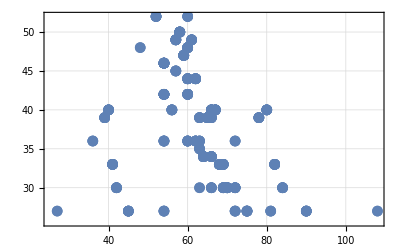

```mathematica
ListPlot[centralizerVsRankResults,PlotMarkers->Automatic,PlotRange->All,GridLines->Automatic,Frame->True]
```

Same as above but including only pairs of generators that don’t contain double Is (b/c those can never give Z-free cosetes)

```mathematica
zFreeCentralizerFromGenerators@{"XXZ"}*zFreeCentralizerFromGenerators@{"XZ"}
```

52

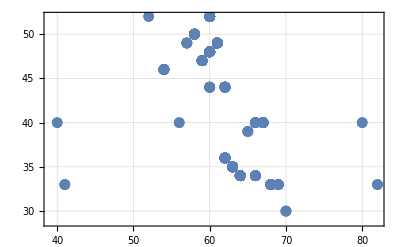

```mathematica
ListPlot[centralizerVsRankResultsNoDoubleI,PlotMarkers->Automatic,PlotRange->All,GridLines->Automatic,Frame->True]
```

#### There’s no pair of generators that gives rank greater than 52:

```mathematica
SelectFirst[pairsOfAbelian5qubitGensNoY,countNonZFullRows@stabiliserFromGenerators@#>52&]//AbsoluteTiming
```

{37.3973,Missing[NotFound]}

```mathematica
stabiliserFromGenerators@{"IIIXZ","XZIII"}//countNonZFullRows
```

48

Can we reproduce the observed max rank numbers with explicit formulas? fix n=3

for t=4, there’s 1 gen, rank is maximised by XXXZ, which gives (3^4-1)/2=40
for t=5, 2 gens, max for {IIIXZ, XXZII}, rank is (3^3-1)/2(3^2-1)/2=52
for t=6, 3 gens, max for {XZIIII, IIXZII, IIIIXZ}, rank ((3^2-1)/2)^3=4^3=64

For n=4, we’d thus get
t=5, (3^5-1)/2=121
t=6, {XXZIII,IIIXXZ}, ((3^3-1)/2)^2=169
t=7, {XZIIIII,IIXZIII,IIIIXXZ}, ((3^2-1)/2)^2((3^3-1)/2)=208
t=8, ((3^2-1)/2)^4=4^4

```mathematica
((3^2-1)/2)^3
```

64

```mathematica
zFreeCentralizerFromGenerators["XXZIII","IIIXXZ"]
zFreeCentralizerFromGenerators["XXXZII","IIIIXZ"]
```

169

160

## n=3, t=6

```mathematica
NotebookDirectory[]
```

C:\Users\utente\OneDrive - UNIPA\projects\QELM&QRC\2025 Monaco - magic\

```mathematica
Import["n3t6_generatori_casibuoni.txt"]
```

Import::nffil: File n3t6_generatori_casibuoni.txt not found during Import.

$Failed